Name: GDM_2D_PA.nb
Author: CCL
Date: October 2014
Description: This script generates a 2D Penrose tiling using the generalized dual method. It can also generate a periodic approximant.

```mathematica
tau=(1+Sqrt[5])/2; (*golden ratio*)
numlines=20;
tolerance=10^-10;
```

```mathematica
a=2Pi/5;
A=tau-1;
r1={1,0,0};
r2={Cos[a],Sin[a],0};
Or3={Cos[2a],Sin[2a],0};
Or4={Cos[3a],Sin[3a],0};
Or5={Cos[4a],Sin[4a],0};
r3=Normalize[-r1+A r2];
r4=Normalize[-A(r1+r2)];
r5=Normalize[-r2+A r1];
starvectors={r1,r2,r3,r4,r5};
origvectors={r1,r2,Or3,Or4,Or5};
numvectors=Length[starvectors];
startuples=Select[Tuples@{Range[numvectors],Range[numvectors]},Less@@#&];
starbasis =Graphics3D[Arrow[{{0,0,0},#}]&/@starvectors,Axes->True];
origstarbasis =Graphics3D[Arrow[{{0,0,0},#}]&/@origvectors,Axes->True];
xyzBasis =Graphics3D[Arrow[{{0,0,0},#}]&/@{{0,0,3},{0,1,0},{1,0,0}},Axes->True];
axes =Graphics3D[Arrow[{{0,0,0},#}]&/@{{1,0,0},{0,1,0},{0,0,1}},Axes->True];
```

```mathematica
PeriodicSeq=Range[-numlines/2,numlines/2];
spacings=PeriodicSeq;
```

```mathematica
Phases={0.01,0.02,0.03,-0.1,0.04};
ShiftedSpacings=Table[i+j,{i,Phases},{j,spacings}]
```

{{-9.99,-8.99,-7.99,-6.99,-5.99,-4.99,-3.99,-2.99,-1.99,-0.99,0.01,1.01,2.01,3.01,4.01,5.01,6.01,7.01,8.01,9.01,10.01},{-9.98,-8.98,-7.98,-6.98,-5.98,-4.98,-3.98,-2.98,-1.98,-0.98,0.02,1.02,2.02,3.02,4.02,5.02,6.02,7.02,8.02,9.02,10.02},{-9.97,-8.97,-7.97,-6.97,-5.97,-4.97,-3.97,-2.97,-1.97,-0.97,0.03,1.03,2.03,3.03,4.03,5.03,6.03,7.03,8.03,9.03,10.03},{-10.1,-9.1,-8.1,-7.1,-6.1,-5.1,-4.1,-3.1,-2.1,-1.1,-0.1,0.9,1.9,2.9,3.9,4.9,5.9,6.9,7.9,8.9,9.9},{-9.96,-8.96,-7.96,-6.96,-5.96,-4.96,-3.96,-2.96,-1.96,-0.96,0.04,1.04,2.04,3.04,4.04,5.04,6.04,7.04,8.04,9.04,10.04}}

```mathematica
maxlength=N[Min[Table[Table[Abs[spacing*Sqrt[2]/starvectors[[i]].{1,1,0}],{spacing,{ShiftedSpacings[[i,1]],ShiftedSpacings[[i,numlines+1]]}}],{i,Range[numvectors]}]]];
```

```mathematica
(*this function finds intersection point of three grid lines, where e_i denotes star vector, and n_i denotes line number*)
FindIntersection[{n1_,e1_},{n2_,e2_},{n3_,e3_}]:=Module[
{p1,p2,p3,d},
p1=n1*e1;
p2=n2*e2;
p3=n3*e3;
d=N[Det[{e1,e2,e3}],{Infinity,150}];
If[d==0,{0,0,0},
Chop[N[1/d*
((p1.e1)Cross[e2,e3]+(p2.e2)Cross[e3,e1]+(p3.e3)Cross[e1,e2]),{Infinity,150}]]]
]
```

```mathematica
(* ULTIMATE FUNCTION *)
(* finds intersections, with tuples of the form
{{m,n},{i,j},{x,y,z}} = {{indices of spacings},{indices of star vectors},{intersection point}} *)
pts=Table[
{{m,n},
{pair[[1]],pair[[2]]},
FindIntersection[{ShiftedSpacings[[pair[[1]],m]],starvectors[[pair[[1]]]]},{ShiftedSpacings[[pair[[2]],n]],starvectors[[pair[[2]]]]},{0,{0,0,1}}]
},
{m,Range[numlines+1]},{n,Range[numlines+1]},{pair,startuples}];
pts=Flatten[pts,2];
pts=pts[[Ordering[pts[[All,3,2]]]]];
```

```mathematica
CountInstances[inlist_,tol_]:=Module[
{poslist,uniqposlist,spacelist,starlist,out,counts,len,uniqlen,counter,curelem,curcompare,i,j},
poslist=inlist[[All,3]];
counts={};
uniqposlist={};
spacelist={};
starlist={};
out={};
len=Length[poslist];
For[i=1,i≤len,i++,
curelem=poslist[[i]];
(*-1 indicates already counted*)
If[TrueQ[curelem==-1],
Continue[];,
uniqposlist=Append[uniqposlist,curelem];
spacelist=Append[spacelist,inlist[[i,1]]];
starlist=Append[starlist,inlist[[i,2]]];
];
counter=1;
For[j=i+1,j≤len,j++,
curcompare=poslist[[j]];
If[TrueQ[curcompare==-1],Continue[];];
If[Norm[poslist[[j]]-curelem]<tol,
poslist[[j]]=-1;(*sets to -1 if counted*)
counter=counter+1;
]
];
counts=Append[counts,counter];
];
uniqlen=Length[uniqposlist];
For[i=1,i≤uniqlen,i++,
out=Append[out,{spacelist[[i]],starlist[[i]],uniqposlist[[i]],counts[[i]]}];
];
out
]
UniqueGridVertices=CountInstances[pts,tolerance];
```

## Find dual of grid intersections, the quasilattice

```mathematica
(*takes a point and finds the indices of the surrounding grid lines*)
FindGridIndices[x_]:=Module[
{gridindices,curindex,curvector,i},
gridindices={};
Do[
curvector=starvectors[[i]];
curindex=Min[Flatten[Position[ShiftedSpacings[[i]],_?(#≥x.curvector&)],1]];
(*returns {} if outside bounds of spacings*)
If[TrueQ[curindex==∞],
gridindices={};
Return[{}];
,
gridindices=Append[gridindices,curindex];
];
,{i,Range[numvectors]}
];
Return[gridindices];
]
```

```mathematica
(*constructs PROTOTILE*)
FindProtoTile[vertex_,i_,j_]:=Module[
{v,tile,pair},
v=Table[vertex+y,{y,
{0,origvectors[[i]],origvectors[[j]],
origvectors[[i]]+origvectors[[j]]
}}];
v=v[[All,{1,2}]];
tile=Graphics[Line[{
{v[[1]],v[[2]]},
{v[[1]],v[[3]]},
{v[[2]],v[[4]]},
{v[[3]],v[[4]]}
}]];
pair={i,j};
{tile,pair}
]
```

```mathematica
(*constructs ZONOTILE*)
eps=10^-4;
UpDown={-1,1};
ProbeIndices=Tuples[{UpDown,UpDown,UpDown,UpDown,UpDown}];
ProbeVectors=N[Table[eps*Normalize[n.starvectors],{n,ProbeIndices}]];

FindZonoTile[vertex_,x_]:=Module[
{GridIndices,UniqueGridIndices,curindex,probe,len,i,j,CurDiff,StarIndex,vertexpair,EdgeIndices,EdgeCoords,VertexCoords,tile,tuple},

(*find grid indices for surrounding open regions*)
GridIndices={};
Do[
curindex=FindGridIndices[x+probe];
If[TrueQ[curindex=={}],
Return[{{},{}}];,
GridIndices=Append[GridIndices,curindex];
];
,{probe,ProbeVectors}
];
UniqueGridIndices=Sort[DeleteDuplicates[GridIndices]];
len=Length[UniqueGridIndices];
(*Print[len];*)

(*go through finding connected vertices, and get vertex coordinates*)
EdgeIndices={};
EdgeCoords={};
VertexCoords=ConstantArray[0,len];
VertexCoords[[1]]=vertex;

For[i=1,i≤len,i++,
For[j=i+1,j≤len,j++,
CurDiff=UniqueGridIndices[[j]]-UniqueGridIndices[[i]];
If[Count[CurDiff,1]==1&&Count[CurDiff,-1]==0,
(*Print[i,", ",j,": ",gridindices[[i]],", ", gridindices[[j]]];*)
StarIndex=Flatten[Position[CurDiff,1]][[1]];
VertexCoords[[j]]=VertexCoords[[i]]+starvectors[[StarIndex]];(*identifies vertex coordinate*)
EdgeIndices=Append[EdgeIndices,{i,j}];
];
];
];

(*construct tile*)
Do[
EdgeCoords=Append[EdgeCoords,{VertexCoords[[vertexpair[[1]]]],VertexCoords[[vertexpair[[2]]]]}];
,{vertexpair,EdgeIndices}
];
tile=Graphics3D[Line[EdgeCoords]];

(*find tuple of star vectors*)
tuple={};
For[i=1,i≤numvectors,i++,
If[Length[Tally[UniqueGridIndices[[All,i]]]]>1,
tuple=Append[tuple,i];
]
];

{tile,tuple}
]
```

```mathematica
FindTile[pt_]:=Module[
{l,m,i,j,x,count,vertex,tile,tuple,v,indices},
l=pt[[1,1]];
m=pt[[1,2]];
i=pt[[2,1]];
j=pt[[2,2]];
x=pt[[3]];
count=pt[[4]];
If[Abs[x[[1]]]<.9maxlength&&Abs[x[[2]]]<.9maxlength&&Abs[x[[3]]]<.9maxlength,
indices=FindGridIndices[x];
If[TrueQ[indices!={}]&&VectorQ[N[indices.starvectors],NumericQ],
vertex=N[indices.starvectors];
If[TrueQ[count==1],
{tile,tuple}=FindProtoTile[vertex,i,j];,
{tile,tuple}=FindZonoTile[vertex,x];
];
Return[{vertex,tile,tuple}]
];
];
Return[];
]
tiles=Select[Table[FindTile[pt],{pt,UniqueGridVertices}],UnsameQ[#,Null]&];
```

```mathematica
(*this function translates a given list of points (x,y,z) such that the center of mass is at the origin*)
 CalculateCOM[pts_]:=Module[
{x,y,z},
x=0;y=0;z=0;
Do[
x+=pt[[1]];
y+=pt[[2]];
z+=pt[[3]];
,
{pt,pts}];
{x,y,z}/Length[pts]
]
```

```mathematica
pts=Flatten[pts,2];
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating (-1/4 - √5/4)\ (-15/16\ (-1 - Power[« 2 »])^2 - 15\ (5/8 - √5/8)) + (1/4 + √5/4)\ (-15/16\ (-1 - Power[« 2 »])^2 - 15\ (5/8 - √5/8)).

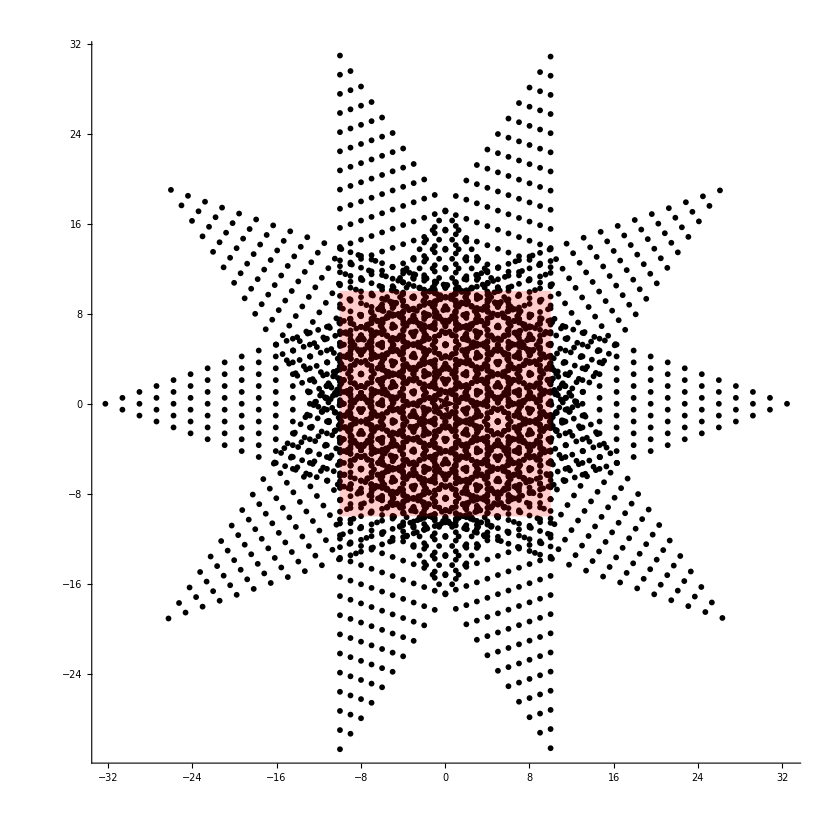

```mathematica
Show[basis,
(*plots n-grid*)
(*Table[Plot[starslopes[[i]]*x+spacings[[j]]/Sin[starangles[[i]]],{x,-maxlength,maxlength},PlotStyle->{Blue,Thin}],{i,1,3},{j,Range[numlines]}],
Table[Graphics[{Blue,Thin,Line[{{spacings[[i]],-maxlength},{spacings[[i]],maxlength}}]}],{i,Range[numlines]}],*)

(*plots points*)
Graphics[{PointSize[0.005],Point[Cases[pts[[All,3]],{_?NumericQ,_?NumericQ,0}][[All,{1,2}]]]}],(*option here gets rid of indeterminate values*)

(*plots window*)
Graphics[{Red,Opacity[0.2],Polygon[{{-maxlength,-maxlength},{-maxlength,maxlength},{maxlength,maxlength},{maxlength,-maxlength},{-maxlength,-maxlength}}]}],

AspectRatio->1]
```

```mathematica
(*From intersections, finds corresponding tiles and their vertices*)
tiles=Select[Table[FindQuasilattice[pt],{pt,pts}],UnsameQ[#,{{},{},{}}]&];
(*translate vertices and tiles so that COM is at origin*)
COM=CalculateCOM[tiles[[All,1]]];
tiles[[All,1]]=Table[pt-COM,{pt,tiles[[All,1]]}];
translate={COM[[{1,2}]],COM[[{1,2}]]};(*since translating edges, ie pairs of vertices*)
Do[
tiles[[i,2,1,1]]=Table[x-translate,{x,tiles[[i,2,1,1,All]]}]
,{i,Length[tiles]}
]
```

```mathematica
(*count number of tiles with starvectors (i,j)*)
Module[
{i,j},
Do[
i=n[[1]]; j=n[[2]];
Print["# tiles with starvectors (", i , ", ", j,"): ",Count[tiles[[All,3]],{i,j}]];
,{n,startuples}
]
]
```

# tiles with starvectors (1, 2): 304

# tiles with starvectors (1, 3): 188

# tiles with starvectors (1, 4): 188

# tiles with starvectors (1, 5): 303

# tiles with starvectors (2, 3): 293

# tiles with starvectors (2, 4): 181

# tiles with starvectors (2, 5): 183

# tiles with starvectors (3, 4): 288

# tiles with starvectors (3, 5): 182

# tiles with starvectors (4, 5): 293

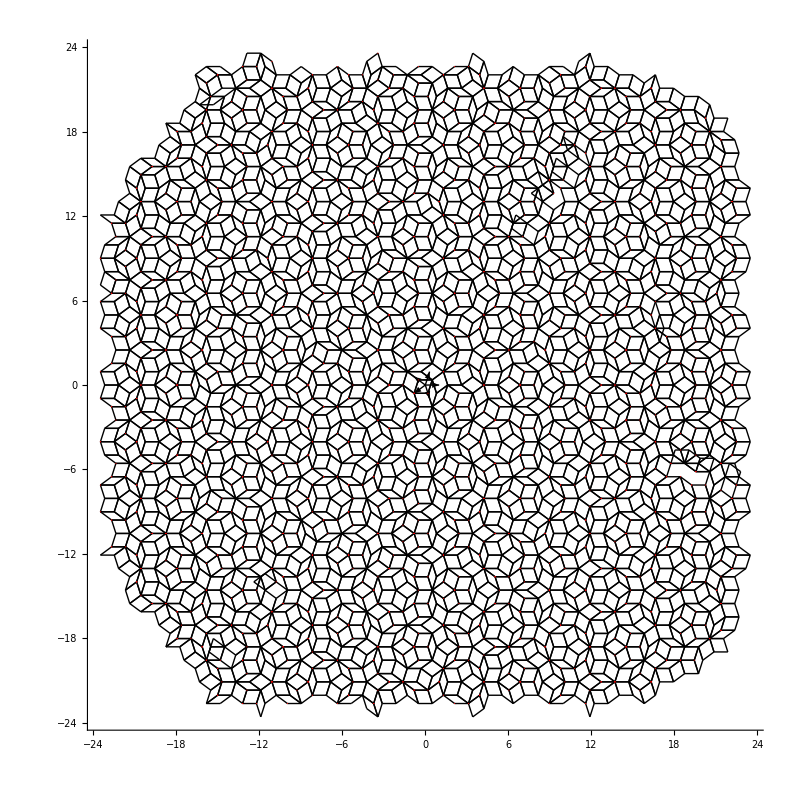

```mathematica
Show[basis,tiles[[All,2]],
Graphics[{PointSize[0.001],Red,Point[tiles[[All,1,{1,2}]]]}]]
```